-1

1

201

{-1,-0.75,-0.5,-0.25,0,0.25,0.5,0.75,1}

{1,0,0,0,0,0,0,0,0}

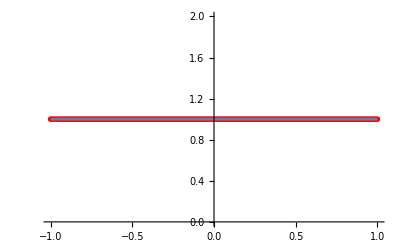

```mathematica
rData = Import["D:\\Storage\\Вуз\\Задания\\Методы вычислений\\labs3kurs\\Interpolation_results\\polyvalues1.txt", "table"];
X = rData[[2]];
a =X[[1]]
b=X[[-1]]
Y = rData[[4]];
m=rData[[1]][[2]]

Points=rData[[6]]
Coeffs=rData[[8]]
n=rData[[7]][[2]];
L[x_]:=Evaluate[Coeffs[[1]]+Sum[Coeffs[[i]]Product[(y-Points[[k]]),{k,1,i-1}],{i,2,n}]]/.y->x;
(*f[x_]:=(4 x^3+2 x^2−4x+2)^(√2)+ArcSin[1/(5+x-x^2)]-5;*)
f[x_]:=1;
Show[ListPlot[Table[{X[[i]],Y[[i]]},{i,m}],PlotStyle->{Red, PointSize[0.01]}],Plot[f[x],{x,a,b}]]
```

```mathematica
Maximize[{Abs[L[x]-f[x]],a<=x<=b},x]
```

{0,{x→0}}

-1

1

101

{-1,-0.75,-0.5,-0.25,0,0.25,0.5,0.75,1}

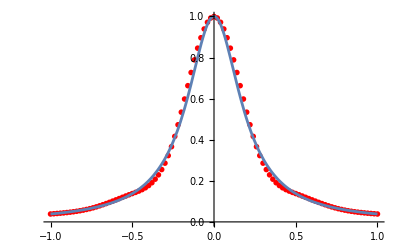

{0.0560742,{x→0.139825}}

```mathematica
rData2 = Import["D:\\Storage\\Вуз\\Задания\\Методы вычислений\\labs3kurs\\Interpolation_results\\splinevalues2.txt", "table"];
X2 = rData2[[2]];
a2 =X2[[1]]
b2=X2[[-1]]
Y2 = rData2[[4]];
m2=rData2[[1]][[2]]

Points2=rData2[[6]]
CoA=rData2[[8]];
CoB=rData2[[10]];
CoC=rData2[[12]];
CoD=rData2[[14]];
n2=rData2[[7]][[2]];
S[x_]:=Piecewise[Table[{CoA[[i]]+CoB[[i]](x-Points2[[i]])+CoC[[i]](x-Points2[[i]])^2+CoD[[i]](x-Points2[[i]])^3,Points2[[i]]<=x<=Points2[[i+1]]},{i,n2}],x];
(*f[x_]:=1/ArcTan[1+10 x^2];*)
f[x_]:=(4 x^3+2 x^2−4x+2)^(√2)+ArcSin[1/(5+x-x^2)]-5;
f[x_]:=1/(1+25 x^2);
Show[ListPlot[Table[{X2[[i]],Y2[[i]]},{i,m2}],PlotStyle->{Red, PointSize[0.01]}],Plot[f[x],{x,a2,b2}]]
```

```mathematica
S[1]
```

0.612652